```mathematica
Manipulate[Plot[{x,g[g[x,r],r]},{x,0,1},AxesLabel->{Subscript[x,n],Subscript[x,n+2]},PlotRange->{{0,1},{0,1}}],{r,0,4}]
```

```mathematica
g[x_,r_]:=r*x*(1-x)
```

```mathematica
f[x_]:=r*x*(1-x)
```

```mathematica
pol=f[f[x]]-x
```

-x+r^2 (1-x) x (1-r (1-x) x)

```mathematica
FullSimplify[pol/(x*(x-(r-1)/r))]
```

-r (1+r (-1+x) (-1+r x))

```mathematica
Solve[x==f[f[x]],x]
```

{{x→0},{x→(-1+r)/r},{x→(r+r^2-r √(-3-2 r+r^2))/(2 r^2)},{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}}

```mathematica
dff=FullSimplify[D[f[f[x]],x]]
```

-r^2 (-1+2 x) (1+2 r (-1+x) x)

```mathematica
FullSimplify[dff/.{x->(r+r^2-r √(-3-2 r+r^2))/(2 r^2)}]
```

4-(-2+r) r

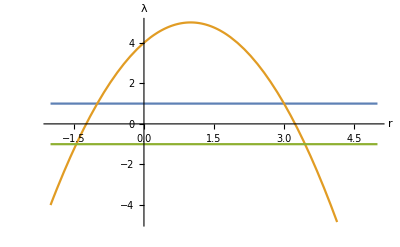

```mathematica
p1=Plot[{1,4-(-2+r) r,-1},{r,-2.,5.},AxesLabel->{r,λ}]
```

```mathematica
Export["eig-2nditerate.jpg",p1,CompressionLevel->0]
```

eig-2nditerate.jpg

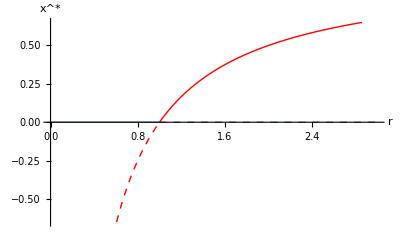

```mathematica
sp1=Show[Plot[0,{r,0,1},PlotRange->{{0,3},{-0.65,0.65}},PlotStyle->Thick,AxesLabel->{r,SuperStar[x]}],Plot[0,{r,1,3},PlotRange->{{0,3},{-0.65,0.65}},PlotStyle->{Thick,Dashed},AxesLabel->{r,SuperStar[x]}],Plot[(r-1)/r,{r,0.1,1},PlotRange->{{0,3},{-0.65,0.65}},PlotStyle->{Thick,Dashed,Red},AxesLabel->{r,SuperStar[x]}],Plot[(r-1)/r,{r,1,3},PlotRange->{{0,3},{-0.65,0.65}},PlotStyle->{Thick,Red},AxesLabel->{r,SuperStar[x]}]]
```

```mathematica
Export["transc-logd.jpg",sp1,CompressionLevel->0]
```

transc-logd.jpg

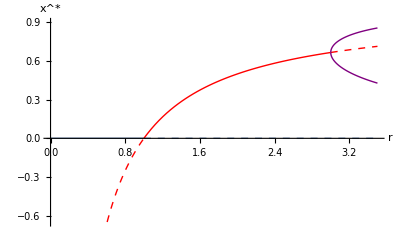

```mathematica
sp2=Show[Plot[0,{r,0,1},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->Thick,AxesLabel->{r,SuperStar[x]}],Plot[0,{r,1,3.5},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->{Thick,Dashed},AxesLabel->{r,SuperStar[x]}],Plot[(r-1)/r,{r,0.1,1},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->{Thick,Dashed,Red},AxesLabel->{r,SuperStar[x]}],Plot[(r-1)/r,{r,1,3},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->{Thick,Red},AxesLabel->{r,SuperStar[x]}],Plot[(r-1)/r,{r,3,3.5},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->{Thick,Dashed,Red},AxesLabel->{r,SuperStar[x]}],Plot[(r+r^2-r √(-3-2 r+r^2))/(2 r^2),{r,3,3.5},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->{Thick,Purple},AxesLabel->{r,SuperStar[x]}],Plot[(r+r^2+r √(-3-2 r+r^2))/(2 r^2),{r,3,3.5},PlotRange->{{0,3.5},{-0.65,0.9}},PlotStyle->{Thick,Purple},AxesLabel->{r,SuperStar[x]}]]
```

```mathematica
Export["flip-logd.jpg",sp2,CompressionLevel->0]
```

flip-logd.jpg

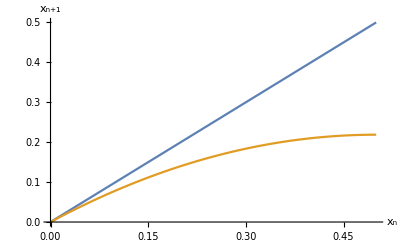

```mathematica
p2=Plot[{x,(7/8)*x(1-x)},{x,0,1/2},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
Export["cobweb-zst-logd.jpg",p2,CompressionLevel->0]
```

cobweb-zst-logd.jpg

```mathematica
s1=RecurrenceTable[{x[n+1]==(7/8)*x[n]*(1-x[n]),x[1]==0.4},x,{n,1,20}];
```

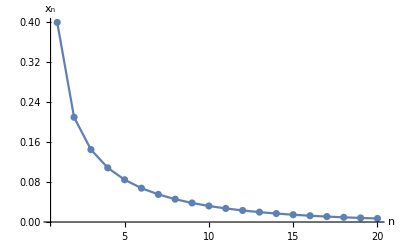

```mathematica
lp1=ListPlot[s1,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["sol-zst-logd.jpg",lp1,CompressionLevel->0]
```

sol-zst-logd.jpg

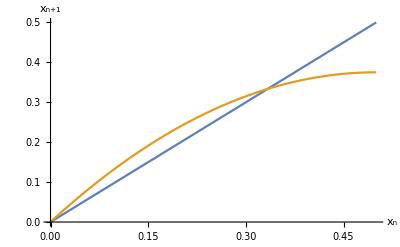

```mathematica
p3=Plot[{x,(3/2)*x(1-x)},{x,0,1/2},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
Export["cobweb-zust-logd.jpg",p3,CompressionLevel->0]
```

cobweb-zust-logd.jpg

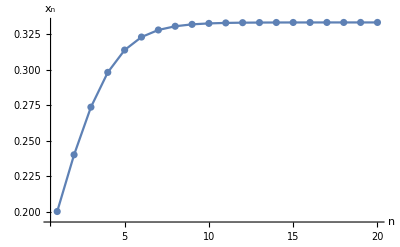

```mathematica
s2=RecurrenceTable[{x[n+1]==(3/2)*x[n]*(1-x[n]),x[1]==0.2},x,{n,1,20}];
lp2=ListPlot[s2,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["sol-zust-logd.jpg",lp2,CompressionLevel->0]
```

sol-zust-logd.jpg

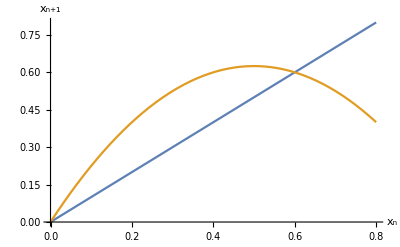

```mathematica
p4=Plot[{x,(5/2)*x(1-x)},{x,0,4/5},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
Export["cobweb-zustosc-logd.jpg",p4,CompressionLevel->0]
```

cobweb-zustosc-logd.jpg

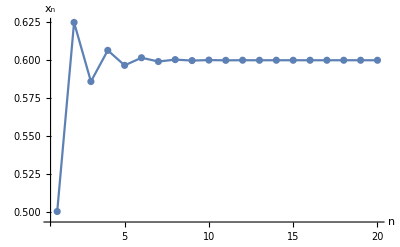

```mathematica
s3=RecurrenceTable[{x[n+1]==(5/2)*x[n]*(1-x[n]),x[1]==0.5},x,{n,1,20}];
lp3=ListPlot[s3,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["sol-zustosc-logd.jpg",lp3,CompressionLevel->0]
```

sol-zustosc-logd.jpg

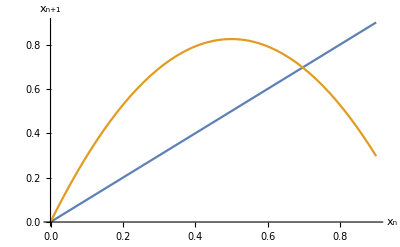

```mathematica
p5=Plot[{x,(33/10)*x(1-x)},{x,0,9/10},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
Export["cobweb-cyctwo-logd.jpg",p5,CompressionLevel->0]
```

cobweb-cyctwo-logd.jpg

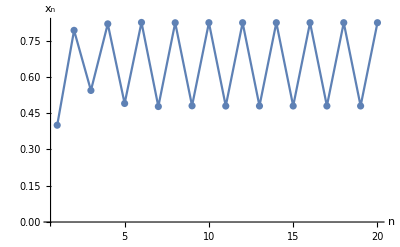

```mathematica
s4=RecurrenceTable[{x[n+1]==(33/10)*x[n]*(1-x[n]),x[1]==0.4},x,{n,1,20}];
lp4=ListPlot[s4,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["sol-cyctwo-logd.jpg",lp4,CompressionLevel->0]
```

sol-cyctwo-logd.jpg